```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
L=xr-xl;
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Cos[2π x/L]
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{1.,1.},{0.9,0.809017},{0.8,0.309017},{0.7,-0.309017},{0.6,-0.809017},{0.5,-1.},{0.4,-0.809017},{0.3,-0.309017},{0.2,0.309017},{0.1,0.809017},{0.,1.}}

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

3.125×10^-7

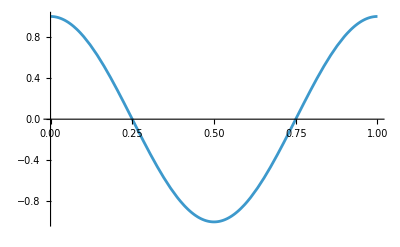

```mathematica
plotexact=Plot[u[x],{x,xl,xr},PlotRange->Full]
```

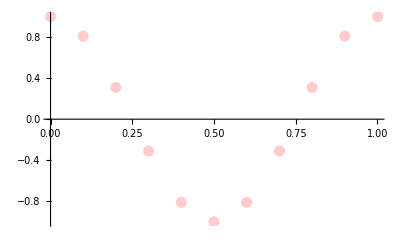

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

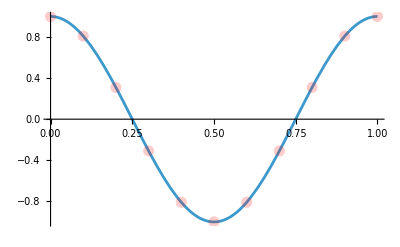

```mathematica
Show[plotexact,plotnum]
```